## Coursework Part 2: Time Dependent Quantum Optics

### Exercise 1: Time dependent Schrödinger equation with the rotating wave approximation

In this exercise we solve the time dependent Shrödinger equation for a two state system of electron spin states in an electromagnetic field. Using the rotating wave approximation we can neglect the terms that oscillate with UnderBar[+](ω + ω_0). That is, we use a time dependent basis state as a possible solution to the TDSE. Then we get a global phase difference but the probability amplitudes remain constant.Also, we assume that the frequency of the light wave or the electromagnetic radiation is at resonance with the frequency of transition between the two energy levels.

```mathematica
PauliMatrix[2]
```

{{0,-ⅈ},{ⅈ,0}}

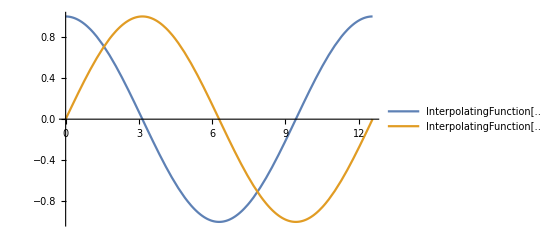

{Abs[InterpolatingFunction[…][t]]^2,Abs[InterpolatingFunction[…][t]]^2}

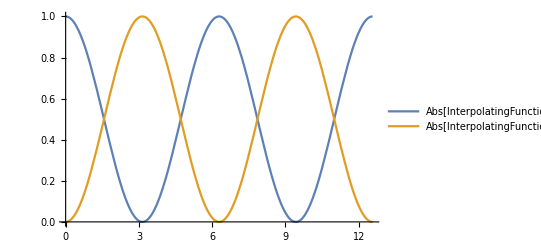

```mathematica
wMatrixRWA=Ω/2 PauliMatrix[2]; (*EM field is in the y direction*)
stateVec=Table[Subscript[c,i][t],{i,2}];
initStateVec={1,0}; (*The particle is at the lower level at t = 0, so Subscript[c, 1](t=0)=1 and Subscript[c, 2](t=0)=0*)
tdseEqnsRWA=Table[{Subscript[c,i]'[t]==-I (wMatrixRWA.stateVec)[[i]],Subscript[c,i][0]==initStateVec[ [i] ]},{i,2}];
tMax=4 Pi;
solRWA=NDSolve[tdseEqnsRWA/. Ω->1,stateVec,{t,0,tMax}];
solFnRWA=stateVec/. First[solRWA];
Plot[solFnRWA,{t,0,tMax}, PlotLegends->"Expressions"]
solFnRWAProb = Abs[solFnRWA]^2
Plot[solFnRWAProb,{t,0,tMax}, PlotLegends->"Expressions"]
```

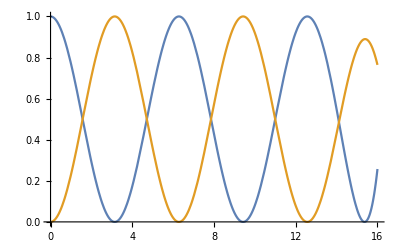

```mathematica
Plot[solFnRWAProb,{t,0,16}]
```

The first plot represents the solution to the TDSE which is oscillatory with a phase difference.The solution contains a real part and an imaginary part. The second plot displays the probability of finding the particle in either of the two energy states. The particle oscillates back and forth between the upper and lower states with Rabi frequency Ω. This means that the interaction of the atom with the electromagnetic field is strong.

```mathematica
PauliMatrix[1]
```

{{0,1},{1,0}}

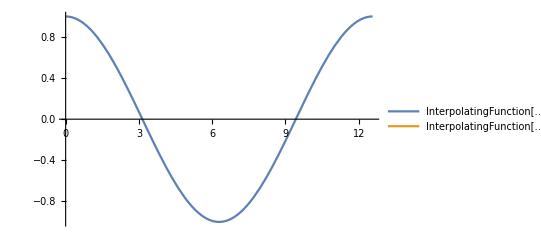

{Abs[InterpolatingFunction[…][t]]^2,Abs[InterpolatingFunction[…][t]]^2}

-Graphics-

```mathematica
wMatrixRWA=Ω/2 PauliMatrix[1];(*EM field in the x direction*)
stateVec=Table[Subscript[c,i][t],{i,2}];
initStateVec={1,0};
tdseEqnsRWA=Table[{Subscript[c,i]'[t]==-I (wMatrixRWA.stateVec)[[i]],Subscript[c,i][0]==initStateVec[ [i] ]},{i,2}];
tMax=4 Pi;
solRWA=NDSolve[tdseEqnsRWA/. Ω->1,stateVec,{t,0,tMax}];
solFnRWA=stateVec/. First[solRWA];
Plot[solFnRWA,{t,0,tMax}, PlotLegends->"Expressions"]
solFnRWAProb = Abs[solFnRWA]^2
Plot[solFnRWAProb,{t,0,tMax},PlotLegends->"Expressions"]
```

When the direction of the EM field is in the x-direction the imaginary part of the solution vanishes and we get a real oscillatory solution to the TDSE. This leaves the probability of finding the particle in either of the two states unaffected. The particle oscillates back and forth between the two states in strong field interaction limit.

### Exercise 2: Time dependent Schrödinger equation in the lab frame

In this exercise, we do not ignore the terms that oscillate between UnderBar[+](ω + ω_0). The separation between the levels is ω_21= ω_2 - ω_1. On resonance ω_21= ω , but if the
atoms have a different frequency, i.e. they have de-tuning Δ from the drive, then  ω_21= ω + Δ. We choose the zero of energy half way between the levels.

```mathematica
Clear[t]
```

```mathematica
wMatrixLab = -ω12/2 PauliMatrix[3] - Ω Cos[ω t] PauliMatrix[2] /. ω12 -> ω +Δ/. { Ω-> 1,ω-> 10,Δ ->0};
```

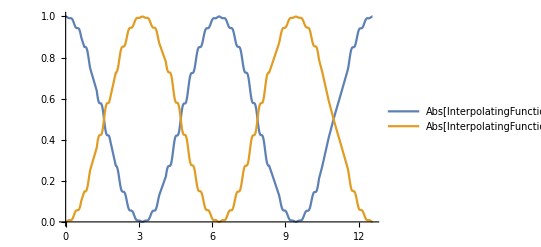

```mathematica
stateVecLab=Table[Subscript[d,i][t],{i,2}];
initStateVecLab={1,0};
tdseEqnsLab=Table[{Subscript[d, i]'[t]==-I (wMatrixLab.stateVecLab)[[i]],Subscript[d, i][0]==initStateVecLab[ [i] ]},{i,2}];
tMax=4 Pi;
solLab=NDSolve[tdseEqnsLab,stateVecLab,{t,0,tMax}];
solFnLab=stateVecLab/. First[solLab];
(* Plot[Re[solFnLab],{t,0,tMax}, PlotLegends->"Expressions"]*)
solFnLabProb = Abs[solFnLab]^2;
Plot[solFnLabProb,{t,0,tMax},PlotLegends->"Expressions",PlotRange->All]
```

We can see that the particle oscillates back and forth between the two energy levels. Which is similar to the previous plot with RWA. The only difference is that the plot is not smooth. This is because we included oscillations between  UnderBar[+](ω + ω_0) in our solution.

### Exercise 3: The Time Dependent Schrodinger Equation with RWA and non-zero de-tuning

clear[t];

solt = MatrixExp[ I t {{ 0, -Ω_R/2},{-Ω_R/2, -Δ}}]// MatrixForm;
Refine[solt /. {√(Δ^2+Ω_R^2)-> Ωgen,( 1/√(Δ^2+Ω_R^2))-> (1/Ωgen)},Δ^2+Ω_R^2>0 ]// MatrixForm

(-(ⅇ^(1/2 ⅈ t (-Δ-Ωgen)) (Δ-Ωgen))/(2 Ωgen)+(ⅇ^(1/2 ⅈ t (-Δ+Ωgen)) (Δ+Ωgen))/(2 Ωgen) | (ⅇ^(1/2 ⅈ t (-Δ-Ωgen)) Ω_R)/(2 Ωgen)-(ⅇ^(1/2 ⅈ t (-Δ+Ωgen)) Ω_R)/(2 Ωgen)
(ⅇ^(1/2 ⅈ t (-Δ-Ωgen)) Ω_R)/(2 Ωgen)-(ⅇ^(1/2 ⅈ t (-Δ+Ωgen)) Ω_R)/(2 Ωgen) | -(ⅇ^(1/2 ⅈ t (-Δ-Ωgen)) (-Δ-Ωgen))/(2 Ωgen)+(ⅇ^(1/2 ⅈ t (-Δ+Ωgen)) (-Δ+Ωgen))/(2 Ωgen))

Plot[Abs[solt]^2, {t, 0, tMax}]

-Graphics-

Refine[solt /. Δ-> 0, Ω_R>0]// MatrixForm

(1/2 ⅇ^(-1/2 ⅈ t Ω_R)+1/2 ⅇ^(1/2 ⅈ t Ω_R) | -1/2 ⅇ^(-1/2 ⅈ t Ω_R)+1/2 ⅇ^(1/2 ⅈ t Ω_R)
-1/2 ⅇ^(-1/2 ⅈ t Ω_R)+1/2 ⅇ^(1/2 ⅈ t Ω_R) | 1/2 ⅇ^(-1/2 ⅈ t Ω_R)+1/2 ⅇ^(1/2 ⅈ t Ω_R))// ExpToTrig // MatrixForm

(Cos[(t Ω_R)/2] | ⅈ Sin[(t Ω_R)/2]
ⅈ Sin[(t Ω_R)/2] | Cos[(t Ω_R)/2])

Changing the phase and drive of the frequency so that the solution matrix can be written in terms of Pauli matrices σ_x and σ_y

Wsimple = {{Δ/2, (-I Ω_R)/2}, {(I Ω_R)/2, -Δ/2}} // MatrixForm

(Δ/2 | -(ⅈ Ω_R)/2
(ⅈ Ω_R)/2 | -Δ/2)

solsimple = MatrixExp[ I t {{Δ/2, (-I Ω_R)/2}, {(I Ω_R)/2, -Δ/2}}] // MatrixForm;
solsimple=Refine[FullSimplify[solsimple, √(Δ^2+Ω_R^2) > 0]]// ExpToTrig // MatrixForm;

solsimple=(Cos[1/2 t √(Δ^2+Ω_R^2)]+(ⅈ Δ Sin[1/2 t √(Δ^2+Ω_R^2)])/(√(Δ^2+Ω_R^2)) | (Sin[1/2 t √(Δ^2+Ω_R^2)] Ω_R)/(√(Δ^2+Ω_R^2))
-(Sin[1/2 t √(Δ^2+Ω_R^2)] Ω_R)/(√(Δ^2+Ω_R^2)) | Cos[1/2 t √(Δ^2+Ω_R^2)]-(ⅈ Δ Sin[1/2 t √(Δ^2+Ω_R^2)])/(√(Δ^2+Ω_R^2)))/. {√(Δ^2+Ω_R^2)-> Ωgen,( 1/√(Δ^2+Ω_R^2))-> (1/Ωgen)}//MatrixForm

(Cos[(t Ωgen)/2]+(ⅈ Δ Sin[(t Ωgen)/2])/Ωgen | (Sin[(t Ωgen)/2] Ω_R)/Ωgen
-(Sin[(t Ωgen)/2] Ω_R)/Ωgen | Cos[(t Ωgen)/2]-(ⅈ Δ Sin[(t Ωgen)/2])/Ωgen)

Plot[Abs[solsimple]^2, {t, 0, tMax}]

-Graphics-

probState2 = Abs[(Sin[(t √(Δ^2+Ω_R^2))/2] Ω_R)/(√(Δ^2+Ω_R^2))]^2;
DensityPlot[probState2,{t,0,tMax},{Δ,-1 10^-6, 1 10^-6}, ColorFunction→"SunsetColors",PlotPoints→100]

-Graphics-

```mathematica
Manipulate[Module[{Ωgen,H,solsimple,probabilities},(*Define generalised Rabi frequency*)Ωgen=Sqrt[Δ^2+ΩR^2];
(*Hamiltonian in rotating frame*)H={{Δ/2,-I ΩR/2},{I ΩR/2,-Δ/2}};
(*Time evolution operator*)solsimple=MatrixExp[I t H]//FullSimplify;
solsimple=solsimple/. {Sqrt[Δ^2+ΩR^2]->Ωgen,(1/Sqrt[Δ^2+ΩR^2])->(1/Ωgen)}//FullSimplify;
solsimple=ExpToTrig[solsimple];
(*Probabilities of being in state 1 or state 2*)probabilities={Abs[solsimple[[1,1]]]^2,Abs[solsimple[[1,2]]]^2};
(*Plot*)Plot[probabilities,{t,0,tMax},PlotLegends->{"|U₁₁(t)|.b2 (stay)","|U₁₂(t)|.b2 (transition)"},AxesLabel->{"t","Probability"},PlotRange->{0,1}]],{{ΩR,1},0.1,5,Appearance->"Labeled"},(*Control for Rabi frequency ΩR*){{Δ,0},-5,5,Appearance->"Labeled"},(*Control for detuning Δ*){{tMax,20},5,50,Appearance->"Labeled"} (*Control for plot duration*)]
```

When the frequency of incident radiation is not resonant with the frequency of transition between the two states, Rabi oscillation frequency increases but the amplitude decreases as the incident radiation is tuned away from resonance.

#### Exercise 4: Hydrogen wavefunction

```mathematica
polarToCartesian = {r -> √(x^2+y^2+z^2), Θ -> ArcCos[z/(√(x^2+y^2+z^2))], ∅ -> ArcTan [y/x]};
ψ[n_, l_, m_] = √((2/n)^3(((n-l-1)!)/(2 n (n +l)!)))ⅇ^(-r/n)((2 r)/n)^l LaguerreL[n-l-1, 2l +1, 2 r/n] × SphericalHarmonicY[l,m,Θ,∅] /. polarToCartesian;
```

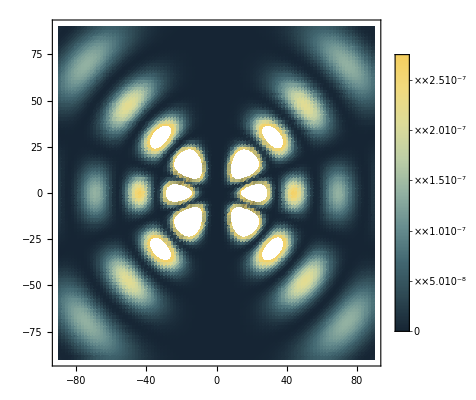

```mathematica
plane = ψ[10, 5, 3]/.{ y->0};
DensityPlot[Abs[plane]^2,{x,-90,90},{z,-90,90},ColorFunction-> "StarryNightColors", PlotPoints->100, PlotLegends->Automatic]
```

### Exercise 5: Time dependent Hydrogen superpositions

basisSet . initStateVec /. superpositionStates

(ⅇ^(-√(x^2+y^2+z^2)))/(√π)

basisSet=Table[ϕ_i,{i,1,2}];
superpositionStates={ϕ_1->ψ[1,0,0],ϕ_2->ψ[2,1,0]};
absAmplitudeMatExp=Abs[basisSet.solsimple.initStateVec/. {Δ->0,Ω_R->1}/. {superpositionStates/.polarToCartesian}]/. y->0

{Abs[{(ⅇ^(-√(x^2+z^2)))/(√π),(ⅇ^(-1/2 √(x^2+z^2)) z)/(4 √(2 π))}.(Cos[t/2] | Sin[t/2]
-Sin[t/2] | Cos[t/2]).{1,0}]}

```mathematica
{Abs[{(ⅇ^(-√(x^2+z^2)))/(√π),(ⅇ^(-1/2 √(x^2+z^2)) z)/(4 √(2 π))}.({{Cos[t/2], Sin[t/2]}, {-Sin[t/2], Cos[t/2]}}).{1,0}]}^2
```

```mathematica
{Abs[(ⅇ^(-√(x^2+z^2)) Cos[t/2])/(√π)-(ⅇ^(-1/2 √(x^2+z^2)) z Sin[t/2])/(4 √(2 π))]^2}//Simplify
```

{(ⅇ^(-2 Re[√(x^2+z^2)]) Abs[-8 Cos[t/2]+√2 ⅇ^(1/2 √(x^2+z^2)) z Sin[t/2]]^2)/(64 π)}

movieFrameMatExp[time_]:=DensityPlot[{(ⅇ^(-2 Re[√(x^2+z^2)]) Abs[-8 Cos[t/2]+√2 ⅇ^(1/2 √(x^2+z^2)) z Sin[t/2]]^2)/(64 π)}, {x, -5,5},{z,-5,5}];(*ffmeg download prompted*)
Table[movieFrameMatExp[time_],{time,0,Pi,Pi/2}]
movieMatExp=Table[movieFrameMatExp[time_],{time,0,tMax,tMax/40}]
Export["rabiMatExp.mov",movieMatExp];

{-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
"rabiMatExp.mov"
```

rabiMatExp.mov

movieFramesolFnLab[time_]:=DensityPlot[{solFnLab}, {t, 0,tMax},{Δ,-1 10^-6,1 10^6}];

Table[movieFramesolFnLab[time_], {time, 0, Pi, Pi/2}]
movieMatExp = Table[movieFramesolFnLab[time_], {time, 0, tMax, tMax/40}]
Export["labFrame.mov", movieMatExp];

{-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* ::Package::*)(*Exercise 5:Time-dependent Hydrogen Superpositions with Visualization Enhancements*)ClearAll[t,x,z,τ,absAmplitudeMatExp,movieFrameMatExp,frames,ΩR,Δ,Ωgen,H,solsimple,initStateVec,basisSet,superpositionStates];

(*Define hydrogen basis states*)
basisSet=Table[Subscript[ϕ,i],{i,1,2}];
superpositionStates={Subscript[ϕ,1]->Exp[-Sqrt[x^2+y^2+z^2]]/Sqrt[π],Subscript[ϕ,2]->(Exp[-(1/2) Sqrt[x^2+y^2+z^2]] z)/(4 Sqrt[2 π])};

initStateVec={1,0};(*Start fully in 1s orbital*)(*Parameters for time evolution*)ΩR=1;(*Rabi frequency*)Δ=0;(*Detuning*)Ωgen=Sqrt[Δ^2+ΩR^2];
H={{Δ/2,-I ΩR/2},{I ΩR/2,-Δ/2}};
solsimple=MatrixExp[I t H]//FullSimplify//ExpToTrig;

(*Absolute value of the evolving wavefunction*)
absAmplitudeMatExp=Abs[(basisSet/. superpositionStates).(solsimple.initStateVec)/. {y->0}];

(*Define density plot frame generator with enhanced resolution and color*)
movieFrameMatExp[τ_,plotPoints_:100]:=Evaluate@DensityPlot[(absAmplitudeMatExp/. t->τ)^2,{x,-5,5},{z,-5,5},PlotRange->All,ColorFunction->"ThermometerColors",PlotPoints->plotPoints,MaxRecursion->2,ColorFunctionScaling->True,FrameLabel->{"x","z"},PlotLabel->Row[{"Time: ",NumberForm[τ,{3,2}]}]];

(*Interactive preview with Manipulate*)
Manipulate[movieFrameMatExp[τ,80],{{τ,0,"Time (τ)"},0,2 π,Appearance->"Labeled"},{{ΩR,1,"Ωₙ (Rabi frequency)"},0.1,5,Appearance->"Labeled"},{{Δ,0,"Detuning Δ"},-5,5,Appearance->"Labeled"},TrackedSymbols:>{τ,ΩR,Δ},Initialization:>(Ωgen=Sqrt[Δ^2+ΩR^2];
H={{Δ/2,-I ΩR/2},{I ΩR/2,-Δ/2}};
solsimple=MatrixExp[I t H]//FullSimplify//ExpToTrig;
absAmplitudeMatExp=Abs[(basisSet/. superpositionStates).(solsimple.initStateVec)/. {y->0}];)]

(*Generate smooth movie frames for export*)
frames=Table[movieFrameMatExp[τ,150],{τ,0,2 π,(2 π)/120}];

(*Export the high-quality movie*)
Export["HydrogenSuperpositionEnhanced.mov",frames,"VideoEncoding"->"MPEG4","FrameRate"->30]
```

Visualization`Core`DensityPlot::ppts: Value of option PlotPoints -> plotPoints is not an integer >= 2.

General::sysffmpeg: Using a limited version of FFmpeg. Install FFmpeg to get more complete codec support.

Export::erropts: The value MPEG4 specified for the option VideoEncoding is invalid.

$Failed

We observe that spin flipping is analogues to how a two level atom interacts with a coherent radiation field. Radiation causes transition between the two energy levels. We considered an electron moving in a central field potential of the nucleus along with the radiation field. The dipole moment and the electron oscillate between the states. When the frequency of incident radiation is not resonant with the frequency of transition between the two states, Rabi oscillation frequency increases but the amplitude decreases as the incident radiation is tuned away from resonance. And when we change the two superposition states the center of charge of the electron shifts. The electron dipole transition rate is zero when the two states violate the selection rules. For a single electron in a hydrogenic system, the selection rules for the quantum numbers n,l,s,and m_S are governed by parity change, conservation of angular momentum and non-interacting photon and electron spins. Photons carry no z-component of momentum when light is linearly polarised along the z-axis. which implies that Δm = 0. When light is polarised in the x-y direction, it is an equal combination of positive and negative circular polarisation, so Δm = UnderBar[+]1. Also, since the there is no interaction between a photon spin and an electron spin the spin quantum number should not change in a transition.